-Graphics-

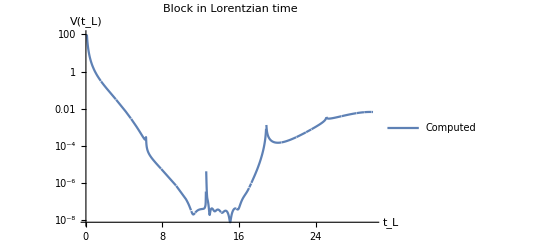

-Graphics-

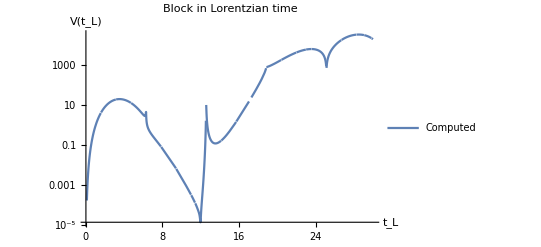

-Graphics-

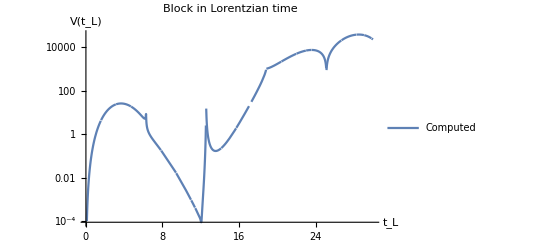

-Graphics-

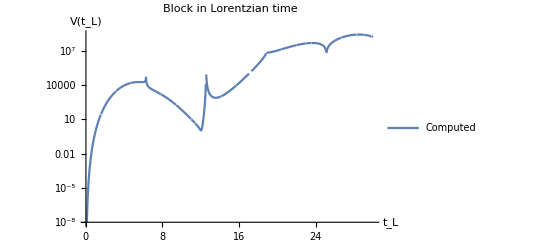

-Graphics-

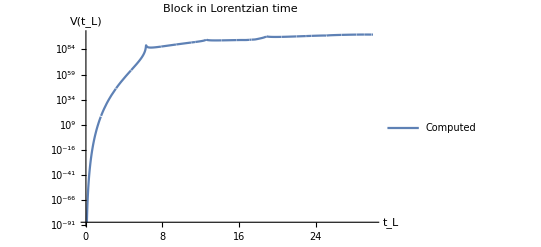

-Graphics-

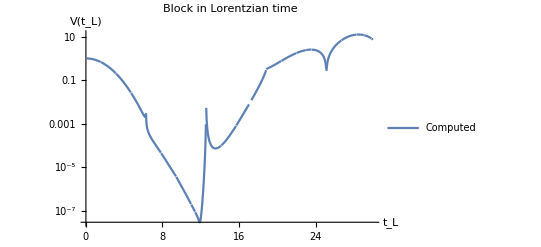

-Graphics-

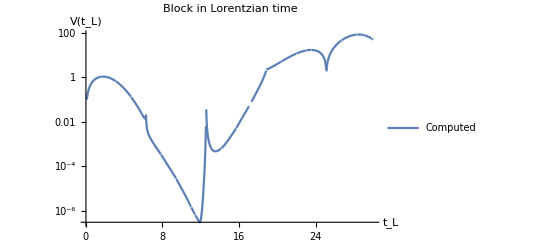

-Graphics-

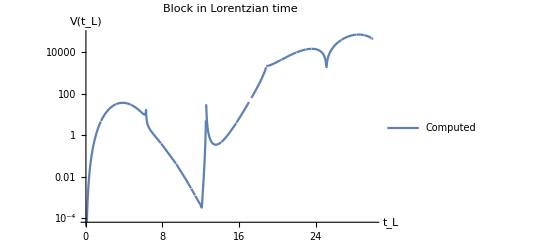

-Graphics-

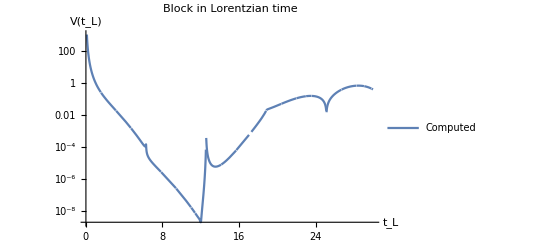

-Graphics-

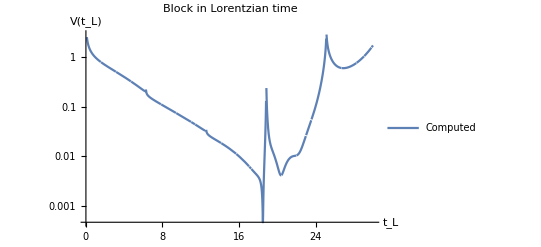

-Graphics-

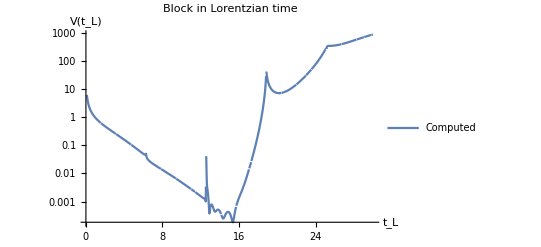

-Graphics-

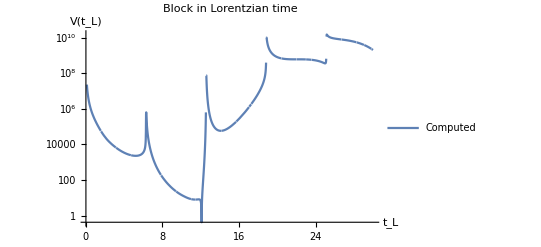

```mathematica
ClearAll["Global`*"];
Get[NotebookDirectory[]<>"Virasoro.m"];

results1=VRun[30,1,3,0,200];
results2=VRun["testruns.txt"];
r=0.99; (*r used in map from q to Subscript[t, L]*)
VPlot[results1,1,1,r];
VPlot[results2,1,1,r];
```

-Graphics-

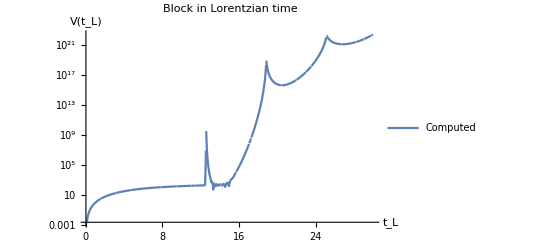

-Graphics-

-Graphics-

```mathematica
ClearAll["Global`*"];
Get[NotebookDirectory[]<>"Virasoro.m"];

results1=VRead[NotebookDirectory[]<>"virasoro_25.3_0.0209_2.11_3_500.txt"];
results2=VRun[518762041/20535000,103233646159/4928400000000,518762041/246420000,21269243681/7885440000,500];
r=0.99; (*r used in map from q to Subscript[t, L]*)
VPlot[results1,1,1,r];
VPlot[results2,1,1,r];
```

-Graphics-

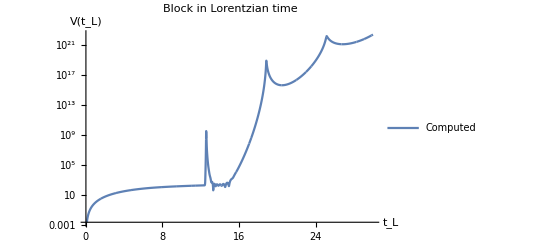

-Graphics-

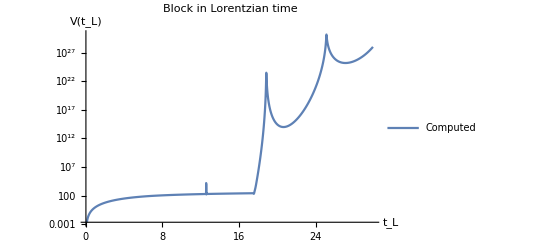

```mathematica
VPlot[results1,1,1,r,PointsPerTL->25];
VPlot[results2,1,1,r,PointsPerTL->25];
```

-Graphics-

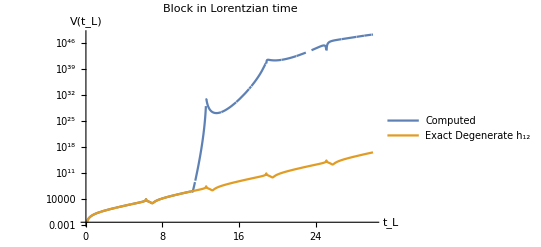

```mathematica
Get[NotebookDirectory[]<>"Virasoro.m"];
VPlot[results,1,1,r,Compare->"12"];
```